```mathematica
(* Data to interpolate *)
ndata=10;
mag=Sqrt[2];
data={RandomReal[{-5,5},{ndata}],RandomReal[{-5,5},{ndata}],RandomReal[{-mag,mag},{ndata}],RandomReal[{-mag,mag},{ndata}]};
```

0.

0.

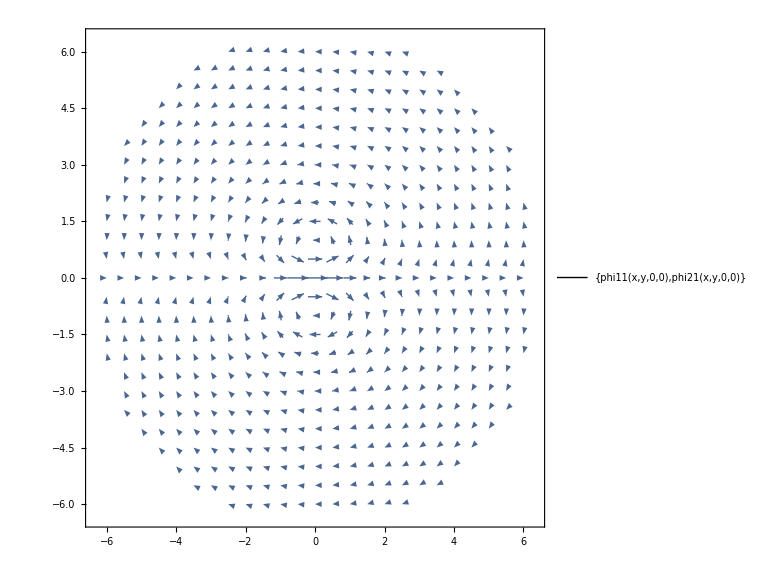

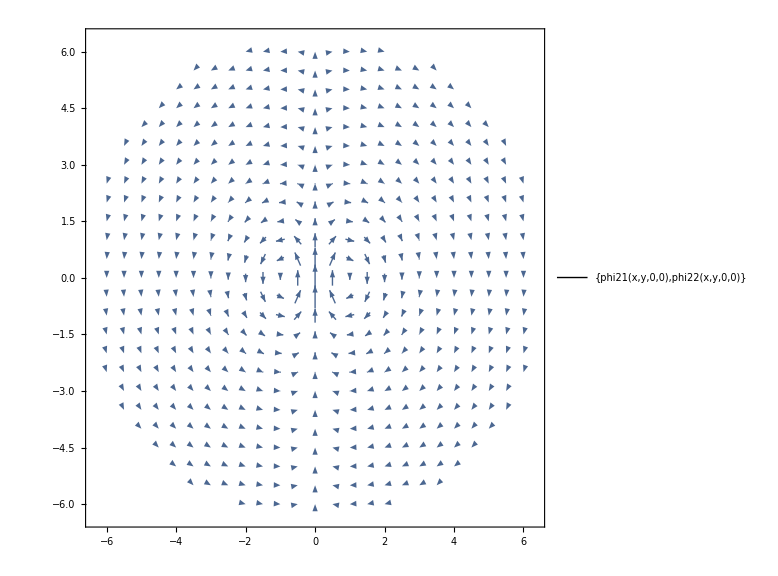

```mathematica
(* Defining functions *)
eps=0.8;
plus[x_]=Piecewise[{{x,x≥0},{0,x<0}}]; (* Needed to define Wendland functions *)

(* Defining RBF functions to occupy *)
f[x_,y_,x0_,y0_] =Exp[-eps^2 ((x-x0)^2+(y-y0)^2)];  (*Gaussian*)
g[x_,y_,x0_,y0_]=Sqrt[1+eps^2 ((x-x0)^2 + (y-y0)^2)];  (*Multiquadric*) 
h[x_,y_,x0_,y0_]=1/Sqrt[1+eps^2 ((x-x0)^2 + (y-y0)^2)]; (*Inverse Multiquadric*)
wendland0[x_,y_,x0_,y0_,s_]= plus[(1-EuclideanDistance[{x,y},{x0,y0}])]^(Floor[s/2]+1); (* Wendland's at k=0 *)

(* Actual basis function *)
psi[x_,y_,x0_,y0_] =f[x,y,x0,y0];

(* Coeficients of Phi matrix *)
phi11[x_,y_,x0_,y0_]=-D[psi[x,y,x0,y0],{y,2}];
phi12[x_,y_,x0_,y0_]=D[psi[x,y,x0,y0],{y,1},{x,1}];
phi21[x_,y_,x0_,y0_]=D[psi[x,y,x0,y0],{x,1},{y,1}];
phi22[x_,y_,x0_,y0_]=-D[psi[x,y,x0,y0],{x,2}];

(* Test to prove (phi11,phi21) and (phi12,phi22) are divergence free fields *)
Div[{phi11[x,y,x0,y0],phi21[x,y,x0,y0]},{x,y}]
Div[{phi12[x,y,x0,y0],phi22[x,y,x0,y0]},{x,y}]

VectorPlot[{phi11[x,y,0,0],phi21[x,y,0,0]},{x,-6,6},{y,-6,6},PlotTheme->"Detailed", ImageSize->Large,VectorPoints->Fine]
VectorPlot[{phi21[x,y,0,0],phi22[x,y,0,0]},{x,-6,6},{y,-6,6},PlotTheme->"Detailed", ImageSize->Large,VectorPoints->Fine]
```

44.4564

6.64788

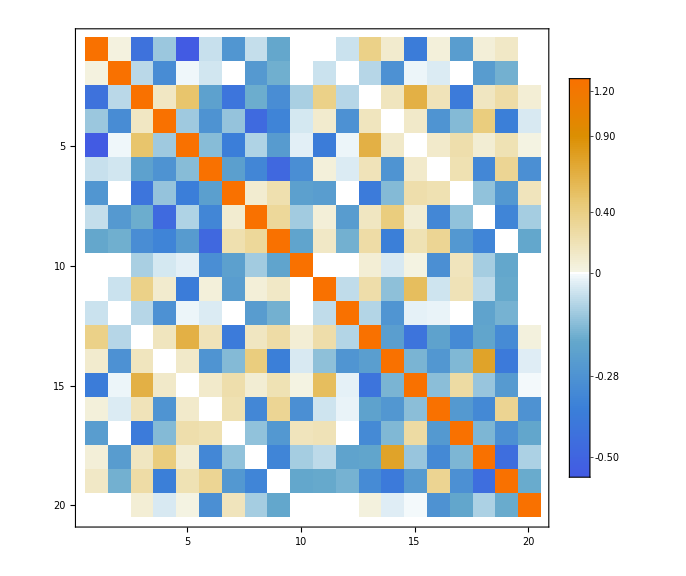

```mathematica
(* Filling matrix A *)
A=RandomReal[{-1,1},{2ndata,2ndata}];

(* Sub matrix A11 *)
For[i=1,i ≤ndata,i++,
For[j=1, j≤ ndata, j++,
A[[i,j]]=Evaluate[phi11[data[[1,i]],data[[2,i]],data[[1,j]],data[[2,j]]]]
]
]
(* Sub matrix A12 *)
For[i=1,i ≤ndata,i++,
For[j=ndata+1, j≤ 2ndata, j++,
A[[i,j]]=Evaluate[phi12[data[[1,i]],data[[2,i]],data[[1,j-ndata]],data[[2,j-ndata]]]]
]
]
(*Sub matrix A21*)
For[i=ndata+1,i ≤2ndata,i++,
For[j=1, j≤ ndata, j++,
A[[i,j]]=Evaluate[phi21[data[[1,i-ndata]],data[[2,i-ndata]],data[[1,j]],data[[2,j]]]]
]
]
(* Sub matrix A22 *)
For[i=ndata+1,i ≤2ndata,i++,
For[j=ndata+1, j≤ 2ndata, j++,A[[i,j]]=Evaluate[phi22[data[[1,i-ndata]],data[[2,i-ndata]],data[[1,j-ndata]],data[[2,j-ndata]]]]
]
]
Det[A]
LinearAlgebra`MatrixConditionNumber[A,Norm->Infinity]
MatrixPlot[A,PlotTheme->"Detailed", ImageSize->Large]
```

```mathematica
(* Vector with vector components at each point. *)
b=Join[data[[3]],data[[4]]];

(* Solve *)
c=LinearSolve[A,b]
```

{0.19393,0.664332,0.820276,-1.27332,-1.07528,1.31914,0.208573,-0.841898,1.04939,-0.0160285,-0.824958,-0.308871,0.980599,0.191044,0.281646,0.30384,-0.0640195,0.727996,-0.638008,-0.300003}

```mathematica
(* Built final interpolating function *)
u=0;
v=0;
For[j=1,j≤ ndata,j++,
u = u+ c[[j]]*phi11[x,y,data[[1,j]],data[[2,j]]]+c[[j+ndata]]*phi12[x,y,data[[1,j]],data[[2,j]]];
v = v+ c[[j]]*phi21[x,y,data[[1,j]],data[[2,j]]]+c[[j+ndata]]*phi22[x,y,data[[1,j]],data[[2,j]]];
]
sx[x_,y_] = u;
sy[x_,y_]=v;
```

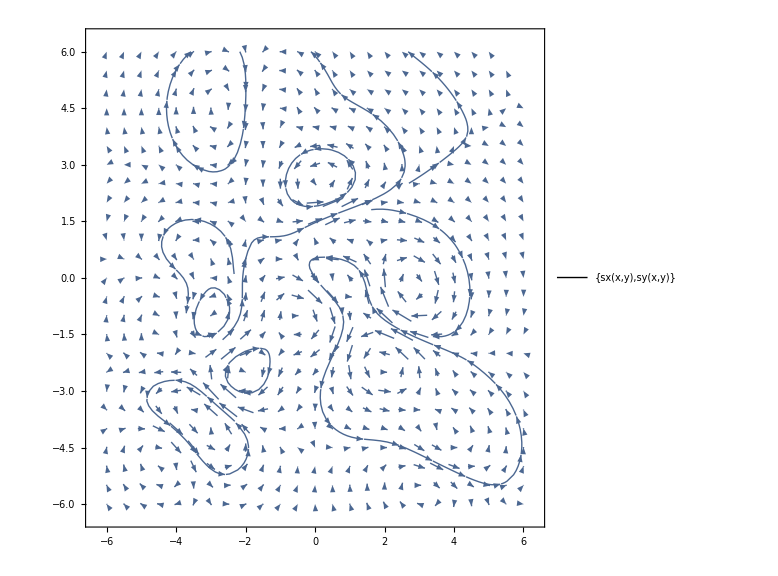

```mathematica
(* Plot of the resulting field *)
VectorPlot[{sx[x,y],sy[x,y]},{x,-6,6},{y,-6,6},PlotTheme->"Detailed", ImageSize->Large,StreamPoints->10]
```

```mathematica
(* Plot of the divergence in the resulting field *)
divs[x_,y_]=Div[{sx[x,y],sy[x,y]},{x,y}];
Plot3D[divs[x,y],{x,-8,8},{y,-8,8},PlotRange->All,PlotTheme->"Detailed", ImageSize->Large]
```

-Graphics3D-